```mathematica
ClearAll["Global`*"]
```

```mathematica
xmin=1;
xmax=3;
```

```mathematica
u[x_]:=1+x^2 
Lu[x_]:=2
gradu[x_]:={2 x}
```

```mathematica
(*check for u*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u_v/solution/nodal_values/u.csv"]
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{f,:0,:1,:2},{10.,3.,0,0},{9.41,2.9,0,0},{8.84,2.8,0,0},{8.29,2.7,0,0},{7.76,2.6,0,0},{7.25,2.5,0,0},{6.76,2.4,0,0},{6.29,2.3,0,0},{5.84,2.2,0,0},{5.41,2.1,0,0},{5.,2.,0,0},{4.61,1.9,0,0},{4.24,1.8,0,0},{3.89,1.7,0,0},{3.56,1.6,0,0},{3.25,1.5,0,0},{2.96,1.4,0,0},{2.69,1.3,0,0},{2.44,1.2,0,0},{2.21,1.1,0,0},{2.,1.,0,0}}

{{3.,10.},{2.9,9.41},{2.8,8.84},{2.7,8.29},{2.6,7.76},{2.5,7.25},{2.4,6.76},{2.3,6.29},{2.2,5.84},{2.1,5.41},{2.,5.},{1.9,4.61},{1.8,4.24},{1.7,3.89},{1.6,3.56},{1.5,3.25},{1.4,2.96},{1.3,2.69},{1.2,2.44},{1.1,2.21},{1.,2.}}

```mathematica
δ=Max[Table[Abs[t[[i,2]]-u[t[[i,1]]]],{i,1,Length[t]}]]
```

3.125×10^-6

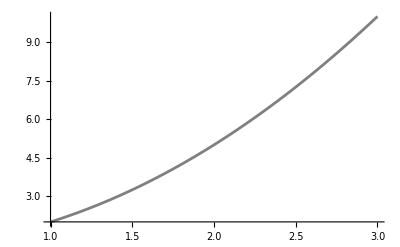

```mathematica
plotexact=Plot[u[x],{x,xmin,xmax},PlotRange->Full,PlotStyle->Gray]
```

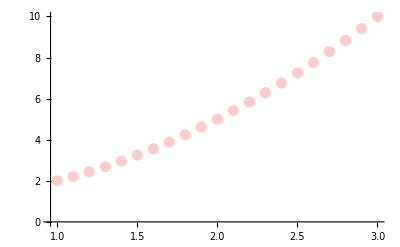

```mathematica
plotnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[0.2],PointSize->0.02}]
```

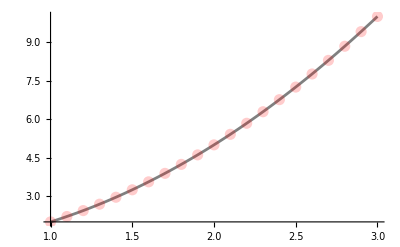

```mathematica
Show[plotexact,plotnum]
```

```mathematica
(*checlk for v*)
```

```mathematica
(*check for v[[1]]*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u_v/solution/nodal_values/v.csv"];
t=Table[{t[[i,4]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,6.},{2.9,5.8},{2.8,5.6},{2.7,5.4},{2.6,5.2},{2.5,5.},{2.4,4.8},{2.3,4.6},{2.2,4.4},{2.1,4.2},{2.,4.},{1.9,3.8},{1.8,3.6},{1.7,3.4},{1.6,3.2},{1.5,3.},{1.4,2.8},{1.3,2.6},{1.2,2.4},{1.1,2.2},{1.,2.}}

```mathematica
δ=Max[Table[Abs[t[[i,2]]-gradu[t[[i,1]]][[1]]],{i,1,Length[t]}]]
```

1.875×10^-6

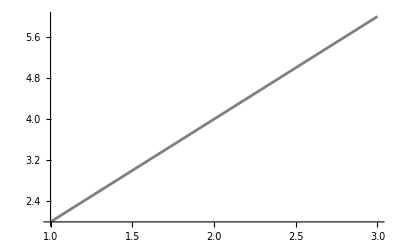

```mathematica
plotexact=Plot[gradu[x][[1]],{x,xmin,xmax},PlotRange->Full,PlotStyle->Gray]
```

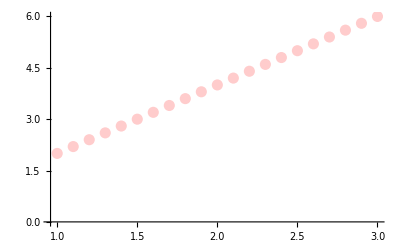

```mathematica
plotnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[0.2],PointSize->0.02}]
```

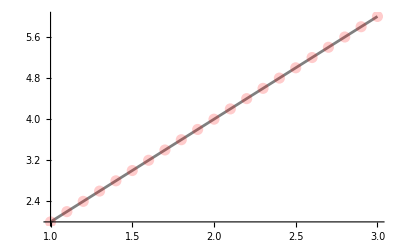

```mathematica
Show[plotexact,plotnum]
```